```mathematica
deltaQ = π * Sum[(ChargeXY[[x,y]][[3]])/Lz,{x,midPtX-1,midPtX+2},{y,1,Ly}]
```

201.086

```mathematica
dataQ = {{0,N[64*π]},{0.01, 201.064370710888},{0.02,201.0668117637175},{0.03,201.069253148827},{0.04,201.07169500657213 },{0.05,201.07413745039446},{0.07,201.07902439823897},{0.1,201.08636035993376}}
```

{{0,201.062},{0.01,201.064},{0.02,201.067},{0.03,201.069},{0.04,201.072},{0.05,201.074},{0.07,201.079},{0.1,201.086}}

```mathematica
Dimensions[dataQ][[1]]
```

8

```mathematica
dataDeltaQ = Table[{dataQ [[i]][[1]],dataQ [[i]][[2]] - dataQ [[1]][[2]]},{i,1,Dimensions[dataQ][[1]]}]
```

{{0,0.},{0.01,0.00244088},{0.02,0.00488193},{0.03,0.00732332},{0.04,0.00976518},{0.05,0.0122076},{0.07,0.0170946},{0.1,0.0244305}}

```mathematica
Fit[dataDeltaQ,{x},x]
```

0.244236 x

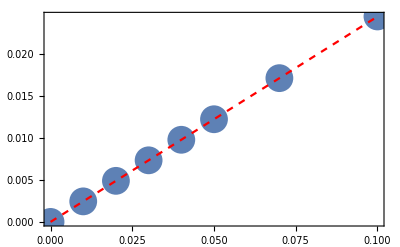

```mathematica
Show[ListPlot[dataDeltaQ,PlotStyle->PointSize[0.05]],Plot[0.24416874645085007 x,{x,0,0.1},PlotStyle->{Dashed,Red}],Frame->True,BaseStyle->18,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```